# deflation.nb : dirac16complex with three deflating degrees of freedom x5, x6, x7

This notebook studies the primordial gravitational field of 6planes.nb in which the three superluminal-time directions x5, x6, x7 are replaced by DEFLATING degrees of freedom. The line element is
ds^2 = Tan[6 H x0]^2 dx0^2 + E^(-2 H x4) Sin[6 H x0]^(-1/3) (dx1^2 + dx2^2 + dx3^2) - dx4^2 - g55 dx5^2 - g66 dx6^2 - g77 dx7^2 ,
g55 = b55 Exp[-a x4], g66 = b66 Exp[-a x4], g77 = b77 Exp[-a x4], a > 0, b55 > 0, b66 > 0, b77 > 0.
x5, x6, x7 stay timelike (the signature remains (4,4) with eta = diag(+1,+1,+1,+1,-1,-1,-1,-1)), so the eight real 16x16 Dirac matrices (T16^A)[0..7] of Pre-gravity6plane.nb remain the Dirac matrices of dirac16complex. Every equation used is written in this notebook and every result is computed below; evaluate from top to bottom. Built on Pre-gravity6plane.nb by P. L. Nash ((C) 2022, GPL).

## Part 0. Coordinates and conventions

The Cartesian coordinates of the project are X = {x0, x1, x2, x3, x4, x5, x6, x7}: x0 = hidden space, x1..x3 = 3-space, x4 = time, x5..x7 = superluminal ("deflating") time. The flat metric is eta4488 = diag(+1,+1,+1,+1,-1,-1,-1,-1), exactly as in Pre-gravity6plane.nb.

```mathematica
ClearAll["Global`*"];
X = {x0, x1, x2, x3, x4, x5, x6, x7};
eta4488 = ArrayFlatten[{{IdentityMatrix[4], 0}, {0, -IdentityMatrix[4]}}];
ID4 = IdentityMatrix[4]; ID8 = IdentityMatrix[8]; ID16 = IdentityMatrix[16];
Diagonal[eta4488]
```

{1,1,1,1,-1,-1,-1,-1}

## Part 1. The eight real 16x16 Dirac matrices (T16^A)[0..7]

### 1.1 Exact construction (identical to Pre-gravity6plane.nb)

Spinor metric sigma (8x8), self-dual (s4by4) and anti-self-dual (t4by4) 4x4 matrices, the six antisymmetric 8x8 matrices, tau[A], taubar[A] = sigma.Transpose[sigma.tau[A]], and finally (T16^A)[A] = [[0, taubar[A]], [tau[A], 0]]. In this notebook the symbol T16A[A] stands for (T16^A)[A] of Pre-gravity6plane.nb (the old notebook used the Notation package to make T16^A a symbol; here we use the plain name T16A to keep the notebook package-free).

```mathematica
sigma = ArrayFlatten[{{ConstantArray[0, {4, 4}], ID4}, {ID4, ConstantArray[0, {4, 4}]}}];
Qa[h_, p_, q_] := Signature[{h, p, q, 4}];
Qb[h_, p_, q_] := ID4[[p, 4]]*ID4[[q, h]] - ID4[[p, h]]*ID4[[q, 4]];
s4by4[h_] := Table[Qa[h, p, q] - Qb[h, p, q], {p, 4}, {q, 4}];   (* self-dual antisymmetric *)
t4by4[h_] := Table[Qa[h, p, q] + Qb[h, p, q], {p, 4}, {q, 4}];   (* anti-self-dual antisymmetric *)
sixAntiSymmetric8by8 = Flatten[{Table[ArrayFlatten[{{0, s4by4[h]}, {s4by4[h], 0}}], {h, 1, 3}],
    Table[ArrayFlatten[{{0, t4by4[h]}, {-t4by4[h], 0}}], {h, 3, 1, -1}]}, 1];
tau[0] = ID8; Do[tau[h] = sixAntiSymmetric8by8[[h]], {h, 1, 6}];
tau[7] = tau[1].tau[2].tau[3].tau[4].tau[5].tau[6];
Do[taubar[h] = sigma.Transpose[sigma.tau[h]], {h, 0, 7}];
Do[T16A[A] = ArrayFlatten[{{0, taubar[A]}, {tau[A], 0}}], {A, 0, 7}];
T16A[8] = Dot @@ Table[T16A[A], {A, 0, 7}];          (* chirality  Gamma = T0 T1 ... T7 *)
sigma16 = T16A[0].T16A[1].T16A[2].T16A[3];           (* spinor metric of dirac16complex *)
PL = (ID16 - T16A[8])/2; PR = (ID16 + T16A[8])/2;    (* chiral projectors *)
SAB = Table[(T16A[A].T16A[B] - T16A[B].T16A[A])/4, {A, 0, 7}, {B, 0, 7}];
Gamma5 = T16A[8];
MatrixForm /@ Table[T16A[A], {A, 0, 7}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

### 1.2 Exact checks

The T^A are real (entries -1, 0, 1) and satisfy T^A T^B + T^B T^A = 2 eta^AB I16; T^0..T^3 are symmetric and T^4..T^7 antisymmetric; Gamma = T^0 T^1 ... T^7 = diag(-I8, I8); sigma16 = T^0 T^1 T^2 T^3 = diag(-sigma, sigma); (sigma16 T^A)^T = -sigma16 T^A, so the Dirac adjoint psibar = psi^dagger sigma16 makes psibar T^A psi a vector and psibar psi a scalar under Spin(4,4), generated by S^AB = (1/4)[T^A, T^B].

```mathematica
<|"T^A real, entries in {-1, 0, 1}" -> SubsetQ[{-1, 0, 1}, Union[Flatten[Table[T16A[A], {A, 0, 7}]]]],
 "T^A T^B + T^B T^A == 2 eta^AB I16" -> (And @@ Flatten[Table[T16A[A].T16A[B] + T16A[B].T16A[A] == 2 eta4488[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]),
 "T^0..T^3 symmetric, T^4..T^7 antisymmetric" -> ((And @@ Table[Transpose[T16A[A]] == T16A[A], {A, 0, 3}]) && (And @@ Table[Transpose[T16A[A]] == -T16A[A], {A, 4, 7}])),
 "Gamma == diag(-I8, I8)" -> (T16A[8] == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]), "sigma16 == diag(-sigma, sigma)" -> (sigma16 == ArrayFlatten[{{-sigma, 0}, {0, sigma}}]),
 "(sigma16 T^A)^T == -sigma16 T^A" -> (And @@ Table[Transpose[sigma16.T16A[A]] == -sigma16.T16A[A], {A, 0, 7}]),
 "[S^AB, T^C] == eta^BC T^A - eta^AC T^B" -> (And @@ Flatten[Table[SAB[[A + 1, B + 1]].T16A[C] - T16A[C].SAB[[A + 1, B + 1]] == eta4488[[B + 1, C + 1]] T16A[A] - eta4488[[A + 1, C + 1]] T16A[B], {A, 0, 7}, {B, 0, 7}, {C, 0, 7}]])|>
```

<|T^A real, entries in {-1, 0, 1}→True,T^A T^B + T^B T^A == 2 eta^AB I16→True,T^0..T^3 symmetric, T^4..T^7 antisymmetric→True,Gamma == diag(-I8, I8)→True,sigma16 == diag(-sigma, sigma)→True,(sigma16 T^A)^T == -sigma16 T^A→True,[S^AB, T^C] == eta^BC T^A - eta^AC T^B→True|>

## Part 2. A small exact Grassmann-algebra engine

dirac16complex has 16 complex components psi_a (a = 0..15) and their complex conjugates psi_a^*; these 32 objects (and their space-time derivatives) are anticommuting Grassmann generators: psi_a psi_b = - psi_b psi_a, in particular psi_a^2 = 0. An element of the Grassmann algebra is stored as an Association  <| {g1,...,gk} -> coefficient |>  with canonically ordered distinct generators. Complex conjugation reverses the order of factors, (theta zeta)^* = zeta^* theta^* for Grassmann elements theta, zeta, the standard convention compatible with Hermitian conjugation of field operators.

```mathematica
gClean[assoc_] := Select[DeleteCases[Map[Together, assoc], 0], True &];
gSortSign[list_] := Module[{ord = Ordering[list]}, If[Length[DeleteDuplicates[list]] < Length[list], {0, {}}, {Signature[ord], list[[ord]]}]];
gFromMono[c_, gens_List] := Module[{s = gSortSign[gens]}, If[s[[1]] == 0 || c === 0, <||>, <|s[[2]] -> s[[1]] c|>]];
gAdd[xs__Association] := gClean[Merge[{xs}, Total]];
gScale[c_, x_Association] := gClean[c # & /@ x];
gMul[x_Association, y_Association] := Module[{res = <||>},
  KeyValueMap[Function[{k1, c1}, KeyValueMap[Function[{k2, c2},
      Module[{s = gSortSign[Join[k1, k2]]}, If[s[[1]] =!= 0, res[s[[2]]] = Lookup[res, Key[s[[2]]], 0] + s[[1]] c1 c2]]], y]], x];
  gClean[res]];
gGen[g_] := <|{g} -> 1|>; gNum[c_] := If[c === 0, <||>, <|{} -> c|>];
gDL[g_, x_Association] := gClean[Association @@ KeyValueMap[Function[{k, c},
     With[{pos = FirstPosition[k, g, {0}][[1]]}, If[pos == 0, Nothing, Delete[k, pos] -> (-1)^(pos - 1) c]]], x]];   (* left derivative *)
gDR[g_, x_Association] := gClean[Association @@ KeyValueMap[Function[{k, c},
     With[{pos = FirstPosition[k, g, {0}][[1]]}, If[pos == 0, Nothing, Delete[k, pos] -> (-1)^(Length[k] - pos) c]]], x]];  (* right derivative *)
gDx[mu_, x_Association, Xs_List] := Module[{res = <||>},   (* total derivative d/dx_mu, Leibniz rule, order preserved *)
  KeyValueMap[Function[{k, c}, res = gAdd[res, gFromMono[D[c, Xs[[mu + 1]]], k]];
     Do[res = gAdd[res, gFromMono[c, ReplacePart[k, i -> (k[[i]] /. gen[t_, a_, d_] :> gen[t, a, Sort[Append[d, mu]]])]]], {i, Length[k]}]], x];
  gClean[res]];
gConjGen[gen[t_, a_, d_]] := gen[If[t === "psi", "psiS", "psi"], a, d];
gConj[x_Association, rule_ : {}] := Module[{res = <||>},
  KeyValueMap[Function[{k, c}, res = gAdd[res, gFromMono[Conjugate[c] /. rule, Reverse[gConjGen /@ k]]]], x]; gClean[res]];
psiF[d_ : {}] := Table[gGen[gen["psi", a, d]], {a, 0, 15}];
psiSF[d_ : {}] := Table[gGen[gen["psiS", a, d]], {a, 0, 15}];
gBil[u_List, M_, v_List] := Module[{res = <||>}, Do[If[M[[i, j]] =!= 0, res = gAdd[res, gScale[M[[i, j]], gMul[u[[i]], v[[j]]]]]], {i, Length[u]}, {j, Length[v]}]; res];
gMatVec[M_, v_List] := Table[Module[{res = <||>}, Do[If[M[[i, j]] =!= 0, res = gAdd[res, gScale[M[[i, j]], v[[j]]]]], {j, Length[v]}]; res], {i, Length[M]}];
gVecAdd[u_List, v_List] := MapThread[gAdd, {u, v}]; gVecScale[c_, u_List] := gScale[c, #] & /@ u;
gZeroQ[x_Association] := Length[gClean[x]] == 0;
gSimplify[x_Association, assum_ : True] := gClean[Simplify[#, assum] & /@ x];
gLinSub[x_Association, rule_] := Module[{res = <||>},
  KeyValueMap[Function[{k, c}, res = gAdd[res, gScale[c, If[k === {}, gNum[1], Fold[gMul, rule /@ k]]]]], x]; res];
p1 = gGen[gen["psi", 1, {}]]; p2 = gGen[gen["psi", 2, {}]]; s1 = gGen[gen["psiS", 1, {}]];
<|"psi1 psi2 + psi2 psi1 = 0" -> gZeroQ[gAdd[gMul[p1, p2], gMul[p2, p1]]], "psi1^2 = 0" -> gZeroQ[gMul[p1, p1]],
 "(psi1^* psi1)^* = psi1^* psi1" -> gZeroQ[gAdd[gConj[gMul[s1, p1]], gScale[-1, gMul[s1, p1]]]]|>
```

<|psi1 psi2 + psi2 psi1 = 0→True,psi1^2 = 0→True,(psi1^* psi1)^* = psi1^* psi1→True|>

## Part 3. Fields, Krein operator, spin connection and curvature tools

```mathematica
psi = psiF[]; psiS = psiSF[]; dpsi[mu_] := psiF[{mu}]; dpsiS[mu_] := psiSF[{mu}];
Sbil = gBil[psiS, sigma16, psi];       (* psibar psi , psibar = psi^dagger.sigma16 *)
K = -I sigma16.T16A[4]; betaKS = -I T16A[4];
spinConnection[Evec_List, Xs_List] := Module[{e = DiagonalMatrix[Evec], Ei, g, gi, Gam, om, n = Length[Xs], Om, gam},
  Ei = Inverse[e]; g = Transpose[e].eta4488.e; gi = Inverse[g];
  Gam = Table[Simplify[(1/2) Sum[gi[[i, l]] (D[g[[l, j]], Xs[[k]]] + D[g[[l, k]], Xs[[j]]] - D[g[[j, k]], Xs[[l]]]), {l, n}]], {i, n}, {j, n}, {k, n}];
  om = Table[Simplify[Sum[e[[A, nu]] (D[Ei[[nu, B]], Xs[[mu]]] + Sum[Gam[[nu, mu, la]] Ei[[la, B]], {la, n}]), {nu, n}]], {mu, n}, {A, n}, {B, n}];
  Om = Table[Simplify[(1/4) Sum[om[[mu, A, B]] eta4488[[A, A]] T16A[A - 1].T16A[B - 1], {A, n}, {B, n}]], {mu, n}];
  gam = Table[Sum[Ei[[nu, A]] T16A[A - 1], {A, n}], {nu, n}];
  <|"Omega" -> Om, "Gamma" -> Gam, "gam" -> gam, "g" -> g|>];
covConst[sc_] := And @@ Flatten[Table[Simplify[D[sc["gam"][[nu]], X[[mu]]] + Sum[sc["Gamma"][[nu, mu, la]] sc["gam"][[la]], {la, 8}] + sc["Omega"][[mu]].sc["gam"][[nu]] - sc["gam"][[nu]].sc["Omega"][[mu]]] == 0 ID16, {mu, 8}, {nu, 8}]];

christoffelG[g_, xs_] := Module[{gi = Simplify[Inverse[g]], n = Length[xs], i, j, k, l},
  Table[Simplify[(1/2) Sum[gi[[i, l]] (D[g[[l, j]], xs[[k]]] + D[g[[l, k]], xs[[j]]] - D[g[[j, k]], xs[[l]]]), {l, n}]], {i, n}, {j, n}, {k, n}]];
riemannG[g_, xs_] := Module[{G = christoffelG[g, xs], n = Length[xs], i, j, k, l, q},
  Table[Simplify[D[G[[i, j, l]], xs[[k]]] - D[G[[i, j, k]], xs[[l]]] + Sum[G[[i, k, q]] G[[q, j, l]] - G[[i, l, q]] G[[q, j, k]], {q, n}]], {i, n}, {j, n}, {k, n}, {l, n}]];
ricciG[g_, xs_] := Module[{R = riemannG[g, xs], n = Length[xs], i, j, l}, Table[Simplify[Sum[R[[i, j, i, l]], {i, n}]], {j, n}, {l, n}]];
einsteinG[g_, xs_] := Module[{Ric = ricciG[g, xs], Rs}, Rs = Simplify[Tr[Inverse[g].Ric]]; Simplify[Ric - (1/2) Rs g]];
kretschmannG[g_, xs_] := Module[{R = riemannG[g, xs], gi = Inverse[g], n = Length[xs], i, j, k, l, a, b, c, e},
  Simplify[Sum[g[[i, a]] R[[a, j, k, l]] Sum[gi[[j, b]] gi[[k, c]] gi[[l, e]] R[[i, b, c, e]], {b, n}, {c, n}, {e, n}], {i, n}, {a, n}, {j, n}, {k, n}, {l, n}]]];
```

The Krein operator K = -I sigma16.T^4 splits dirac16complex into two mirror sectors psi_+ = P+ psi and psi_- = P- psi, P+- = (I16 +- K)/2. K is Hermitian with K^2 = I16 and eigenvalues +1 and -1 (8 each); it commutes with T^0, ..., T^4 and anticommutes with T^5, T^6, T^7; sigma16 = K beta with beta = -I T^4. Consequently the terms built from the directions x0..x4 have no cross terms between the sectors, psibar T^A d_A psi = psi_+^dagger beta T^A d_A psi_+ - psi_-^dagger beta T^A d_A psi_- (A = 0..4) and psibar psi = psi_+^dagger beta psi_+ - psi_-^dagger beta psi_-: the K = -1 sector enters the Lagrangian with the opposite sign. For a mode psi = E^(-I omega x4) u the canonical energy density (1/2)(psibar T^4 d4 psi - (d4 psibar) T^4 psi) equals omega psi^dagger K psi, so a mode of the K = -1 sector carries the opposite energy of the same mode of the K = +1 sector. The energy of a universe is called its mass: K = +1 is the +mass sector and K = -1 the -mass sector.

```mathematica
Pp = (ID16 + K)/2; Pm = (ID16 - K)/2;
uv = Array[ur, 16] + I Array[ui, 16]; psiM = E^(-I om x4) uv;
enM = (1/2) (Conjugate[psiM].sigma16.T16A[4].D[psiM, x4] - Conjugate[D[psiM, x4]].sigma16.T16A[4].psiM);
<|"K Hermitian, K^2 == I16" -> ((ConjugateTranspose[K] == K) && (K.K == ID16)), "eigenvalues of K" -> Counts[Eigenvalues[K]],
 "[K, T^A] == 0 (A = 0..4)" -> (And @@ Table[K.T16A[A] == T16A[A].K, {A, 0, 4}]), "{K, T^A} == 0 (A = 5, 6, 7)" -> (And @@ Table[K.T16A[A] == -T16A[A].K, {A, 5, 7}]),
 "sigma16 == K beta, beta = -I T^4" -> (sigma16 == K.betaKS),
 "P+ sigma16 T^A P- == 0, P+ sigma16 T^A P+ == P+ beta T^A P+, P- sigma16 T^A P- == -P- beta T^A P- (A = 0..4)" -> (And @@ Flatten[Table[{Pp.sigma16.T16A[A].Pm == 0 ID16, Pp.sigma16.T16A[A].Pp == Pp.betaKS.T16A[A].Pp, Pm.sigma16.T16A[A].Pm == -Pm.betaKS.T16A[A].Pm}, {A, 0, 4}]]),
 "P+ sigma16 P- == 0, P+ sigma16 P+ == P+ beta P+, P- sigma16 P- == -P- beta P-" -> ((Pp.sigma16.Pm == 0 ID16) && (Pp.sigma16.Pp == Pp.betaKS.Pp) && (Pm.sigma16.Pm == -Pm.betaKS.Pm)),
 "mode energy density (1/2)(psibar T^4 d4 psi - (d4 psibar) T^4 psi) == omega psi^dagger K psi" -> (Simplify[ComplexExpand[enM - om Conjugate[psiM].K.psiM]] === 0)|>
```

<|K Hermitian, K^2 == I16→True,eigenvalues of K→<|-1→8,1→8|>,[K, T^A] == 0 (A = 0..4)→True,{K, T^A} == 0 (A = 5, 6, 7)→True,sigma16 == K beta, beta = -I T^4→True,P+ sigma16 T^A P- == 0, P+ sigma16 T^A P+ == P+ beta T^A P+, P- sigma16 T^A P- == -P- beta T^A P- (A = 0..4)→True,P+ sigma16 P- == 0, P+ sigma16 P+ == P+ beta P+, P- sigma16 P- == -P- beta P-→True,mode energy density (1/2)(psibar T^4 d4 psi - (d4 psibar) T^4 psi) == omega psi^dagger K psi→True|>

## Part 4. The deflating degrees of freedom x5, x6, x7

Vielbein e^A_mu = diag(e_0, ..., e_7) with e_0 = Tan[6 H x0], e_1 = e_2 = e_3 = E^(-H x4) Sin[6 H x0]^(-1/6), e_4 = 1, e_5 = Sqrt[g55], e_6 = Sqrt[g66], e_7 = Sqrt[g77]; metric g_mu nu = eta_AB e^A_mu e^B_nu, so the x5, x6, x7 entries are -g55, -g66, -g77. A coordinate interval dx5 has proper size L5 = Sqrt[g55] dx5 = Sqrt[b55] E^(-a x4/2) dx5: it shrinks by the factor E^(-1) every Delta x4 = 2/a (deflation rate d ln L5/dx4 = -a/2).

```mathematica
z0 = 6 H x0;
gjj = {b55 Exp[-a x4], b66 Exp[-a x4], b77 Exp[-a x4]};          (* g55, g66, g77 *)
eDefl = {Tan[z0], E^(-H x4) Sin[z0]^(-1/6), E^(-H x4) Sin[z0]^(-1/6), E^(-H x4) Sin[z0]^(-1/6), 1, Sqrt[b55] E^(-a x4/2), Sqrt[b66] E^(-a x4/2), Sqrt[b77] E^(-a x4/2)};   (* e_j = Sqrt[gjj] *)
gDefl = DiagonalMatrix[eDefl^2 Diagonal[eta4488]];
assumD = H > 0 && 0 < x0 < Pi/(12 H) && a > 0 && b55 > 0 && b66 > 0 && b77 > 0 && Element[X, Reals] && Element[{m, lam}, Reals];
sqrtgD = Simplify[Times @@ eDefl, assumD];        (* all e_A > 0 in the domain *)
<|"e_j^2 == gjj (j = 5,6,7)" -> (Simplify[eDefl[[6 ;; 8]]^2 - gjj] == {0, 0, 0}), "Sqrt|g|^2 == |det g|" -> (Simplify[sqrtgD^2 - Abs[Det[gDefl]], assumD] == 0),
 "metric diagonal g_00..g_77" -> Simplify[Diagonal[gDefl], assumD], "x5,x6,x7 entries equal -g55,-g66,-g77" -> (Simplify[Diagonal[gDefl][[6 ;; 8]] + gjj, assumD] == {0, 0, 0}),
 "proper size per unit dx5" -> Simplify[Sqrt[gjj[[1]]], assumD], "deflation rate d ln L5/dx4" -> Simplify[D[Log[Sqrt[gjj[[1]]]], x4], assumD],
 "volume factor of the deflating 3-space" -> Simplify[Sqrt[Times @@ gjj], assumD], "Sqrt|g|" -> sqrtgD|>
```

<|e_j^2 == gjj (j = 5,6,7)→True,Sqrt|g|^2 == |det g|→True,metric diagonal g_00..g_77→{Tan[6 H x0]^2,ⅇ^(-2 H x4)/Sin[6 H x0]^(1/3),ⅇ^(-2 H x4)/Sin[6 H x0]^(1/3),ⅇ^(-2 H x4)/Sin[6 H x0]^(1/3),-1,-b55 ⅇ^(-a x4),-b66 ⅇ^(-a x4),-b77 ⅇ^(-a x4)},x5,x6,x7 entries equal -g55,-g66,-g77→True,proper size per unit dx5→√(b55 ⅇ^(-a x4)),deflation rate d ln L5/dx4→-a/2,volume factor of the deflating 3-space→√(b55 b66 b77 ⅇ^(-3 a x4)),Sqrt|g|→ⅇ^(-3/2 (a+2 H) x4) Sec[6 H x0] √(b55 b66 b77 Sin[6 H x0])|>

## Part 5. Curvature of the deflation field

Ricci tensor R_jl = R^i_jil, scalar R = g^jl R_jl, Einstein tensor G_mu nu = R_mu nu - (1/2) R g_mu nu (the diagonal mixed components G^mu_mu and every non-zero off-diagonal Ricci component R_mu nu, mu < nu, are shown), and the Kretschmann scalar R_abcd R^abcd, computed with the diagonal-metric formula Sum g_aa g^bb g^cc g^dd (R^a_bcd)^2. We check that these invariants do not depend on x4 and compute their behaviour at x0 -> 0. The pure deflation field (x0..x3 flat and x4 undeformed, ds^2 = dx0^2+dx1^2+dx2^2+dx3^2-dx4^2-g55 dx5^2-g66 dx6^2-g77 dx7^2) isolates the effect of the deflating degrees of freedom; its curvature invariants are constants.

```mathematica
kretschmannDiag[g_, xs_] := Module[{R = riemannG[g, xs], n = Length[xs], gd = Diagonal[g], i, j, k, l},
  Simplify[Sum[gd[[i]]/(gd[[j]] gd[[k]] gd[[l]]) R[[i, j, k, l]]^2, {i, n}, {j, n}, {k, n}, {l, n}]]];
RicD = ricciG[gDefl, X]; RsD = Simplify[Tr[Inverse[gDefl].RicD], assumD]; KD = kretschmannDiag[gDefl, X];
GmixD = Simplify[Diagonal[Inverse[gDefl].(RicD - (1/2) RsD gDefl)], assumD];
<|"Ricci scalar" -> RsD, "mixed Einstein tensor G^0_0 ... G^7_7" -> GmixD,
 "non-zero off-diagonal Ricci components {mu, nu} -> R_mu nu (mu < nu)" -> Select[Flatten[Table[If[i < j, {i - 1, j - 1} -> Simplify[RicD[[i, j]], assumD], Nothing], {i, 8}, {j, 8}]], #[[2]] =!= 0 &],
 "G_04 == R_04 (because g_04 = 0)" -> (Simplify[(RicD - (1/2) RsD gDefl)[[1, 5]] - RicD[[1, 5]], assumD] === 0),
 "Kretschmann scalar R_abcd R^abcd" -> KD, "R, G^mu_mu, R_04 and R_abcd R^abcd do not depend on x4" -> FreeQ[{RsD, GmixD, Simplify[RicD[[1, 5]], assumD], KD}, x4],
 "x0^4 R as x0 -> 0" -> Limit[x0^4 RsD, x0 -> 0, Direction -> "FromAbove", Assumptions -> H > 0 && a > 0],
 "x0^8 R_abcd R^abcd as x0 -> 0" -> Limit[x0^8 KD, x0 -> 0, Direction -> "FromAbove", Assumptions -> H > 0 && a > 0]|>
```

<|Ricci scalar→3/8 (3 (a^2+3 a H-32 H^2)-4 (a^2+3 a H+32 H^2) Cos[12 H x0]+a (a+3 H) Cos[24 H x0]) Csc[6 H x0]^4,mixed Einstein tensor G^0_0 ... G^7_7→{-3/16 (-4 (a^2+3 a H+6 H^2) Cos[12 H x0]+(a^2+3 a H+2 H^2) (3+Cos[24 H x0])) Csc[6 H x0]^4,-3/16 (3 a^2+6 a H-64 H^2-4 (a^2+2 a H+20 H^2) Cos[12 H x0]+a (a+2 H) Cos[24 H x0]) Csc[6 H x0]^4,-3/16 (3 a^2+6 a H-64 H^2-4 (a^2+2 a H+20 H^2) Cos[12 H x0]+a (a+2 H) Cos[24 H x0]) Csc[6 H x0]^4,-3/16 (3 a^2+6 a H-64 H^2-4 (a^2+2 a H+20 H^2) Cos[12 H x0]+a (a+2 H) Cos[24 H x0]) Csc[6 H x0]^4,3/4 (a^2+4 H^2)-3/16 (3 (a^2+3 a H-32 H^2)-4 (a^2+3 a H+32 H^2) Cos[12 H x0]+a (a+3 H) Cos[24 H x0]) Csc[6 H x0]^4,-3/32 (3 (a^2+4 a H-64 H^2)-4 (a^2+4 a H+64 H^2) Cos[12 H x0]+a (a+4 H) Cos[24 H x0]) Csc[6 H x0]^4,-3/32 (3 (a^2+4 a H-64 H^2)-4 (a^2+4 a H+64 H^2) Cos[12 H x0]+a (a+4 H) Cos[24 H x0]) Csc[6 H x0]^4,-3/32 (3 (a^2+4 a H-64 H^2)-4 (a^2+4 a H+64 H^2) Cos[12 H x0]+a (a+4 H) Cos[24 H x0]) Csc[6 H x0]^4},non-zero off-diagonal Ricci components {mu, nu} -> R_mu nu (mu < nu)→{{0,4}→-3 H^2 Cot[6 H x0]},G_04 == R_04 (because g_04 = 0)→True,Kretschmann scalar R_abcd R^abcd→3/2 (a^4+6 a^2 H^2+8 H^4+H^4 (1245+108 Cos[12 H x0]-Cos[24 H x0]) Cot[6 H x0]^4 Csc[6 H x0]^4+8 H^4 Cos[12 H x0]^2 Csc[6 H x0]^8),R, G^mu_mu, R_04 and R_abcd R^abcd do not depend on x4→True,x0^4 R as x0 -> 0→-7/(108 H^2),x0^8 R_abcd R^abcd as x0 -> 0→85/(69984 H^4)|>

```mathematica
gPure = DiagonalMatrix[{1, 1, 1, 1, -1, -gjj[[1]], -gjj[[2]], -gjj[[3]]}];
RicP = ricciG[gPure, X]; RsP = Simplify[Tr[Inverse[gPure].RicP], assumD];
<|"pure deflation: Ricci scalar" -> RsP, "pure deflation: Kretschmann scalar" -> kretschmannDiag[gPure, X],
 "pure deflation: mixed Einstein tensor" -> Simplify[Diagonal[Inverse[gPure].(RicP - (1/2) RsP gPure)], assumD]|>
```

<|pure deflation: Ricci scalar→3 a^2,pure deflation: Kretschmann scalar→(3 a^4)/2,pure deflation: mixed Einstein tensor→{-(3 a^2)/2,-(3 a^2)/2,-(3 a^2)/2,-(3 a^2)/2,-(3 a^2)/4,-(3 a^2)/4,-(3 a^2)/4,-(3 a^2)/4}|>

Geometry of the deflating block. In the pure deflation field every Riemann component with an index in x0..x3 vanishes (x0..x3 span flat R^4), and the block (x4, x5, x6, x7) with metric -dx4^2 - g55 dx5^2 - g66 dx6^2 - g77 dx7^2 is maximally symmetric: R_abcd = (a^2/4)(g_ac g_bd - g_ad g_bc). With w = (2/a) E^(a x4/2) and yj = Sqrt[bjj] xj (j = 5, 6, 7) its metric becomes -(4/a^2)(dw^2 + dy5^2 + dy6^2 + dy7^2)/w^2. The metric of the block is negative definite and minus it is the Poincare upper-half-space metric (4/a^2)(dw^2 + dy5^2 + dy6^2 + dy7^2)/w^2 of the hyperbolic 4-space H^4 of radius 2/a: the time x4 and the three deflating degrees of freedom form an H^4 whose four directions are all timelike. The infinite past x4 -> -Infinity is the boundary w = 0, the infinite future x4 -> +Infinity is w -> Infinity. This is why R = 12/(2/a)^2 = 3 a^2 and R_abcd R^abcd = 24/(2/a)^4 = 3 a^4/2 are constant.

```mathematica
Y4 = {x4, x5, x6, x7}; g4 = DiagonalMatrix[{-1, -gjj[[1]], -gjj[[2]], -gjj[[3]]}];
RP = riemannG[gPure, X]; R4 = riemannG[g4, Y4];
R4low = Table[Sum[g4[[i, p]] R4[[p, j, k, l]], {p, 4}], {i, 4}, {j, 4}, {k, 4}, {l, 4}];   (* R_abcd = g_ap R^p_bcd *)
xOfY = {(2/a) Log[a w/2], y5/Sqrt[b55], y6/Sqrt[b66], y7/Sqrt[b77]}; JacY = D[xOfY, {{w, y5, y6, y7}}];
gW = Simplify[Transpose[JacY].(g4 /. x4 -> xOfY[[1]]).JacY, assumD && w > 0];
<|"Riemann components with an index in x0..x3 all vanish" -> AllTrue[Flatten[Table[If[Min[i, j, k, l] <= 4, RP[[i, j, k, l]], 0], {i, 8}, {j, 8}, {k, 8}, {l, 8}]], # === 0 &],
 "(x4..x7) block: R_abcd == (a^2/4)(g_ac g_bd - g_ad g_bc)" -> (Simplify[R4low - Table[(a^2/4) (g4[[i, k]] g4[[j, l]] - g4[[i, l]] g4[[j, k]]), {i, 4}, {j, 4}, {k, 4}, {l, 4}], assumD] === ConstantArray[0, {4, 4, 4, 4}]),
 "metric of the block in (w, y5, y6, y7)" -> gW, "equals -(4/a^2) I4/w^2" -> (Simplify[gW + (4/a^2)/w^2 IdentityMatrix[4], assumD && w > 0] === ConstantArray[0, {4, 4}])|>
```

<|Riemann components with an index in x0..x3 all vanish→True,(x4..x7) block: R_abcd == (a^2/4)(g_ac g_bd - g_ad g_bc)→True,metric of the block in (w, y5, y6, y7)→{{-4/(a^2 w^2),0,0,0},{0,-4/(a^2 w^2),0,0},{0,0,-4/(a^2 w^2),0},{0,0,0,-4/(a^2 w^2)}},equals -(4/a^2) I4/w^2→True|>

## Part 6. Geodesics: deflation turns world lines back in the time x4

For a world line moving in (x4, x5) the momentum p5 = g_55 dx5/dlambda = -g55 dx5/dlambda is conserved, so dx5/dlambda = -(p5/b55) E^(a x4) grows exponentially. Normalising -(dx4/dlambda)^2 - g55 (dx5/dlambda)^2 = -1 gives (dx4/dlambda)^2 = 1 - (p5^2/b55) E^(a x4): the world line reaches a TURNING POINT x4* = (1/a) Log[b55/p5^2] and cannot proceed to later x4. We also check the x4 geodesic equation d^2x4/dlambda^2 = -Gamma^4_55 (dx5/dlambda)^2. In the coordinates w = (2/a) E^(a x4/2), y5 = Sqrt[b55] x5 of the hyperbolic block (Part 5) the world line is a semicircle (y5 - y5c)^2 + w^2 = w*^2 of radius w* = 2 Sqrt[b55]/(a |p5|) standing on the boundary w = 0, because (dw/dy5)^2 = (w*^2 - w^2)/w^2; its top w = w* is the turning point x4*. The world line comes from x4 -> -Infinity and returns to x4 -> -Infinity.

```mathematica
x5dot = p5/(-gjj[[1]]);
x4dot2 = Simplify[1 - gjj[[1]] x5dot^2, assumD];
Gam45 = christoffelG[DiagonalMatrix[{-1, -gjj[[1]]}], {x4, x5}];
wOf = (2/a) E^(a x4/2); wstar = 2 Sqrt[b55]/(a p5);
<|"dx5/dlambda" -> Simplify[x5dot], "(dx4/dlambda)^2" -> x4dot2, "turning point x4*" -> Simplify[x4 /. First[Solve[x4dot2 == 0, x4, Reals]], assumD && p5 > 0],
 "x4 geodesic equation satisfied: (1/2) d(x4dot^2)/dx4 == -Gamma^4_55 x5dot^2" -> Simplify[(1/2) D[x4dot2, x4] == -Gam45[[1, 2, 2]] x5dot^2, assumD],
 "semicircle in (y5, w): (dw/dy5)^2 == (w*^2 - w^2)/w^2" -> (Simplify[(D[wOf, x4]^2 x4dot2)/(Sqrt[b55] x5dot)^2 - (wstar^2 - wOf^2)/wOf^2, assumD && p5 > 0] === 0),
 "w at the turning point == w* = 2 Sqrt[b55]/(a p5)" -> (Simplify[(wOf /. x4 -> Log[b55/p5^2]/a) - wstar, assumD && p5 > 0] === 0)|>
```

<|dx5/dlambda→-(ⅇ^(a x4) p5)/b55,(dx4/dlambda)^2→1-(ⅇ^(a x4) p5^2)/b55,turning point x4*→Log[b55/p5^2]/a,x4 geodesic equation satisfied: (1/2) d(x4dot^2)/dx4 == -Gamma^4_55 x5dot^2→True,semicircle in (y5, w): (dw/dy5)^2 == (w*^2 - w^2)/w^2→True,w at the turning point == w* = 2 Sqrt[b55]/(a p5)→True|>

## Part 7. Euler-Lagrange equations of dirac16complex in the deflation field

L = Sqrt|g| [ (1/2)(psibar gamma^mu D_mu psi - (D_mu psibar) gamma^mu psi) - m psibar psi - (lam/2)(psibar psi)^2 ], gamma^mu = E_A^mu T^A, D_mu psi = d_mu psi + Omega_mu psi, Omega_mu = (1/4) omega_mu^A_B T_A T^B with T_A = eta_AB T^B, omega_mu^A_B = e^A_nu (d_mu E_B^nu + Gamma^nu_{mu la} E_B^la). The Euler-Lagrange equations are derived with left Grassmann derivatives and compared with the matrix form; the mass-sign maps C psi = Gamma psi^* and P1 psi(x) = T^1 psi(R1 x) are checked as exact Grassmann identities.

```mathematica
scD = spinConnection[eDefl, X]; OmD = scD["Omega"]; gamD = scD["gam"];
LD = gScale[sqrtgD, gAdd[gScale[1/2, gAdd @@ Table[gBil[psiS, sigma16.gamD[[mu + 1]], dpsi[mu]], {mu, 0, 7}]], gScale[1/2, gBil[psiS, Simplify[sigma16.Sum[gamD[[mu]].OmD[[mu]], {mu, 8}]], psi]],
    gScale[-1/2, gAdd @@ Table[gBil[dpsiS[mu], sigma16.gamD[[mu + 1]], psi], {mu, 0, 7}]], gScale[1/2, gBil[psiS, Simplify[sigma16.Sum[OmD[[mu]].gamD[[mu]], {mu, 8}]], psi]], gScale[-m, Sbil], gScale[-lam/2, gMul[Sbil, Sbil]]]];
realRuleD = {Conjugate[m] -> m, Conjugate[lam] -> lam, Conjugate[H] -> H, Conjugate[a] -> a, Conjugate[b55] -> b55, Conjugate[b66] -> b66, Conjugate[b77] -> b77, Conjugate[x0] -> x0, Conjugate[x4] -> x4};
ELD = Table[gSimplify[gAdd[gDL[gen["psiS", aa, {}], LD], gScale[-1, gAdd @@ Table[gDx[mu, gDL[gen["psiS", aa, {mu}], LD], X], {mu, 0, 7}]]], assumD], {aa, 0, 15}];
DpsiD = Fold[gVecAdd, Table[gMatVec[gamD[[mu + 1]], gVecAdd[dpsi[mu], gMatVec[OmD[[mu + 1]], psi]]], {mu, 0, 7}]];
expectedD = gMatVec[sqrtgD sigma16, gVecAdd[gVecAdd[DpsiD, gVecScale[-m, psi]], gVecScale[-lam, Table[gMul[Sbil, psi[[b]]], {b, 16}]]]];
spinD = Simplify[Sum[gamD[[mu]].OmD[[mu]], {mu, 8}], assumD];
ruleC[gen["psi", aa_, d_]] := gAdd @@ Table[gScale[Gamma5[[aa + 1, b + 1]], gGen[gen["psiS", b, d]]], {b, 0, 15}];
ruleC[gen["psiS", aa_, d_]] := gAdd @@ Table[gScale[Gamma5[[aa + 1, b + 1]], gGen[gen["psi", b, d]]], {b, 0, 15}];
ruleP[gen[t_, aa_, d_]] := gScale[(-1)^Count[d, 1], gAdd @@ Table[gScale[T16A[1][[aa + 1, b + 1]], gGen[gen[t, b, d]]], {b, 0, 15}]];
<|"gamma^mu covariantly constant" -> covConst[scD], "L real" -> gZeroQ[gSimplify[gAdd[gConj[LD, realRuleD], gScale[-1, LD]], assumD]],
 "EL == Sqrt|g| sigma16 (gamma^mu D_mu psi - m psi - lam (psibar psi) psi)" -> (And @@ MapThread[gZeroQ[gSimplify[gAdd[#1, gScale[-1, #2]], assumD]] &, {ELD, expectedD}]),
 "E_A^A factors (gamma^mu = E_A^mu T^A)" -> Simplify[1/eDefl, assumD],
 "spin-connection term gamma^mu Omega_mu: coefficients of T^0..T^7" -> Table[Simplify[Tr[spinD.T16A[A]] eta4488[[A + 1, A + 1]]/16, assumD], {A, 0, 7}],
 "L[Gamma psi^*] == L(m->-m)[psi]" -> gZeroQ[gSimplify[gAdd[gLinSub[LD, ruleC], gScale[-1, LD /. m -> -m]], assumD]],
 "L[T1 psi(R1 x)] == L(m->-m)[psi](R1 x)" -> gZeroQ[gSimplify[gAdd[gLinSub[LD, ruleP], gScale[-1, LD /. m -> -m]], assumD]]|>
```

<|gamma^mu covariantly constant→True,L real→True,EL == Sqrt|g| sigma16 (gamma^mu D_mu psi - m psi - lam (psibar psi) psi)→True,E_A^A factors (gamma^mu = E_A^mu T^A)→{Cot[6 H x0],ⅇ^(H x4) Sin[6 H x0]^(1/6),ⅇ^(H x4) Sin[6 H x0]^(1/6),ⅇ^(H x4) Sin[6 H x0]^(1/6),1,ⅇ^((a x4)/2)/(√b55),ⅇ^((a x4)/2)/(√b66),ⅇ^((a x4)/2)/(√b77)},spin-connection term gamma^mu Omega_mu: coefficients of T^0..T^7→{-3/2 H Cot[6 H x0]^2,0,0,0,-3/4 (a+2 H),0,0,0},L[Gamma psi^*] == L(m->-m)[psi]→True,L[T1 psi(R1 x)] == L(m->-m)[psi](R1 x)→True|>

Hence the field equation of dirac16complex in the deflation field is, explicitly,
Cot[6Hx0] T^0 d0 psi + E^(H x4) Sin[6Hx0]^(1/6) (T^1 d1 + T^2 d2 + T^3 d3) psi + T^4 d4 psi + E^(a x4/2) (T^5 d5/Sqrt[b55] + T^6 d6/Sqrt[b66] + T^7 d7/Sqrt[b77]) psi - (3/2) H Cot[6Hx0]^2 T^0 psi - (3/2)(H + a/2) T^4 psi = (m + lam psibar psi) psi .
The deflating directions enter through the GROWING factors E^(a x4/2)/Sqrt[bjj], and the deflation adds the friction term -(3a/4) T^4 psi.

## Part 8. Universes in the deflation field: dispersion, turning point and critical deflation rate

Universes are mode functions: c-number solutions of the linear part of the field equation (lam = 0; in a mean-field (Kohn-Sham) treatment of the quartic term with constant rho_s = <psibar psi>, m stands for the effective mass m + lam rho_s). The exact rescaling psi = F chi, F = Sin[6Hx0]^(1/4) E^(3(a + 2H) x4/4), removes both spin-connection (friction) terms, because gamma^mu d_mu F + F gamma^mu Omega_mu = 0. For a mode chi = Exp[I (k0 x0 + k1 x1 + k2 x2 + k3 x3 + q5 x5 + q6 x6 + q7 x7 - omega x4)] u with frozen (adiabatic) coefficients c_A = 1/e_A, the field equation gives (I S - I omega T^4 - m) u = 0 with S = Sum_(A != 4) c_A k_A T^A (k_5, k_6, k_7 = q5, q6, q7). Because S anticommutes with T^4 and S^2 = Sum_(A != 4) eta_AA (c_A k_A)^2 I16, solutions exist iff omega^2 = m^2 + S^2:
omega^2 = m^2 + Cot[6Hx0]^2 k0^2 + E^(2 H x4) Sin[6Hx0]^(1/3) (k1^2+k2^2+k3^2) - E^(a x4) (q5^2/b55 + q6^2/b66 + q7^2/b77).
Momentum along a deflating (timelike) direction LOWERS omega^2 with weight E^(a x4). For k1=k2=k3=0, omega^2 = m^2 + Cot[6Hx0]^2 k0^2 - E^(a x4) (q5^2/b55 + q6^2/b66 + q7^2/b77) decreases strictly with x4, so the universe turns from oscillating (omega^2 > 0) to exponentially growing (omega^2 < 0) at the unique point x4* = (1/a) Log[(m^2 + Cot[6Hx0]^2 k0^2)/(q5^2/b55 + q6^2/b66 + q7^2/b77)]. With 3-space momentum the late-time sign of omega^2 is decided by the competition E^(2 H x4) versus E^(a x4): the critical deflation rate is a_c = 2H. At a = 2H exactly, omega^2 = m^2 + Cot[6Hx0]^2 k0^2 + E^(2 H x4) (Sin[6Hx0]^(1/3) (k1^2+k2^2+k3^2) - q5^2/b55 - q6^2/b66 - q7^2/b77), and the late-time sign is the sign of the bracket.

```mathematica
FD = Sin[z0]^(1/4) E^(3 (a + 2 H) x4/4);
cD = Simplify[1/eDefl, assumD]; kv = {k0, k1, k2, k3, 0, q5, q6, q7};
Sslash = Sum[cD[[A + 1]] kv[[A + 1]] T16A[A], {A, 0, 7}];
omega2 = Simplify[m^2 + Sum[eta4488[[A + 1, A + 1]] (cD[[A + 1]] kv[[A + 1]])^2, {A, 0, 7}], assumD];
qq = q5^2/b55 + q6^2/b66 + q7^2/b77; om0 = omega2 /. {k1 -> 0, k2 -> 0, k3 -> 0}; x4starD = Log[(m^2 + k0^2 Cot[z0]^2)/qq]/a;
om2H = Simplify[omega2 /. a -> 2 H, assumD]; C2H = Simplify[Coefficient[Expand[om2H], E^(2 H x4)], assumD];
sampleD = {H -> 1, x0 -> 1/10, m -> 1, k0 -> 0, k1 -> 1, k2 -> 0, k3 -> 0, q5 -> 1, q6 -> 0, q7 -> 0, b55 -> 1, b66 -> 1, b77 -> 1};
<|"psi = F chi removes the spin connection: gamma^mu d_mu F + F gamma^mu Omega_mu == 0" -> (Simplify[Sum[gamD[[mu]] D[FD, X[[mu]]], {mu, 8}] + FD spinD, assumD] == 0 ID16),
 "S^2 == Sum eta_AA (c_A k_A)^2 I16" -> (Simplify[Sslash.Sslash - Sum[eta4488[[A + 1, A + 1]] (cD[[A + 1]] kv[[A + 1]])^2, {A, 0, 7}] ID16, assumD] == 0 ID16),
 "{S, T^4} = 0" -> (Simplify[Sslash.T16A[4] + T16A[4].Sslash] == 0 ID16), "omega^2" -> omega2,
 "k1=k2=k3=0: omega^2 == m^2 + k0^2 Cot^2 - E^(a x4) Sum qj^2/bjj" -> (Simplify[om0 - (m^2 + k0^2 Cot[z0]^2 - E^(a x4) qq), assumD] === 0),
 "d omega^2/dx4 == -a E^(a x4) Sum qj^2/bjj < 0" -> (Simplify[D[om0, x4] + a E^(a x4) qq, assumD] === 0),
 "omega^2 == 0 at x4* = Log[(m^2 + k0^2 Cot^2)/Sum qj^2/bjj]/a" -> (Simplify[om0 /. x4 -> x4starD, assumD && m > 0 && qq > 0] === 0),
 "a = 2H: coefficient C2H of E^(2 H x4) in omega^2" -> C2H, "a = 2H: omega^2 == m^2 + k0^2 Cot^2 + C2H E^(2 H x4)" -> (Simplify[om2H - (m^2 + k0^2 Cot[z0]^2 + C2H E^(2 H x4)), assumD] === 0),
 "late time, H = 1, a = 3 > 2H" -> Limit[omega2 /. sampleD /. a -> 3, x4 -> Infinity], "late time, H = 1, a = 2 = 2H" -> Limit[omega2 /. sampleD /. a -> 2, x4 -> Infinity],
 "late time, H = 1, a = 1 < 2H" -> Limit[omega2 /. sampleD /. a -> 1, x4 -> Infinity]|>
```

<|psi = F chi removes the spin connection: gamma^mu d_mu F + F gamma^mu Omega_mu == 0→True,S^2 == Sum eta_AA (c_A k_A)^2 I16→True,{S, T^4} = 0→True,omega^2→m^2-(ⅇ^(a x4) q5^2)/b55-(ⅇ^(a x4) q6^2)/b66-(ⅇ^(a x4) q7^2)/b77+k0^2 Cot[6 H x0]^2+ⅇ^(2 H x4) (k1^2+k2^2+k3^2) Sin[6 H x0]^(1/3),k1=k2=k3=0: omega^2 == m^2 + k0^2 Cot^2 - E^(a x4) Sum qj^2/bjj→True,d omega^2/dx4 == -a E^(a x4) Sum qj^2/bjj < 0→True,omega^2 == 0 at x4* = Log[(m^2 + k0^2 Cot^2)/Sum qj^2/bjj]/a→True,a = 2H: coefficient C2H of E^(2 H x4) in omega^2→-q5^2/b55-q6^2/b66-q7^2/b77+(k1^2+k2^2+k3^2) Sin[6 H x0]^(1/3),a = 2H: omega^2 == m^2 + k0^2 Cot^2 + C2H E^(2 H x4)→True,late time, H = 1, a = 3 > 2H→-∞,late time, H = 1, a = 2 = 2H→-∞,late time, H = 1, a = 1 < 2H→∞|>

Exact evolution in the pure deflation field (x0..x3 flat, e_4 = 1, e_j = Sqrt[bjj] E^(-a x4/2)). There gamma^mu Omega_mu = -(3a/4) T^4, and with psi = E^(3 a x4/4) Exp[I (k1 x1 + q5 x5)] chi(x4) the linear field equation gamma^mu D_mu psi = m psi becomes exactly E^(3 a x4/4) Exp[I (k1 x1 + q5 x5)] T^4 (chi' - M chi) = 0, i.e. chi' = M chi with M = T^4 (I k1 T^1 + I q5 c(x4) T^5 - m), c(x4) = E^(a x4/2)/Sqrt[b55] (checked in the next cell). We start at x4 = -8 in a positive-frequency universe of the K = +1 (+mass) sector, solve numerically (a = b55 = k = m = 1, q = 1/2, so x4* = Log[8] = 2.079) and record the norm chi^dagger chi and the fraction in the K = -1 (-mass) sector.

```mathematica
ePure = {1, 1, 1, 1, 1, Sqrt[b55] E^(-a x4/2), Sqrt[b66] E^(-a x4/2), Sqrt[b77] E^(-a x4/2)};
scP = spinConnection[ePure, X];
chiS = Array[ch[#][x4] &, 16]; phaseP = E^(3 a x4/4) E^(I (k1 x1 + q5 x5)); psiP = phaseP chiS;
DpsiP = Sum[scP["gam"][[mu]].(D[psiP, X[[mu]]] + scP["Omega"][[mu]].psiP), {mu, 8}] - m psiP;     (* gamma^mu D_mu psi - m psi *)
Mchi = T16A[4].(I k1 T16A[1] + I q5 E^(a x4/2)/Sqrt[b55] T16A[5] - m ID16);
aN = 1; bN = 1; kN = 1; mN = 1; qN = 1/2; x4star = Log[(mN^2 + kN^2)/(qN^2/bN)]/aN;
h0 = -kN T16A[4].T16A[1] - I mN T16A[4];             (* instantaneous Hamiltonian at c = 0 ; chi' = -I h chi *)
Kp = (ID16 + K)/2; Km = (ID16 - K)/2;
{vals0, vecs0} = Eigensystem[N[Kp.h0.Kp + 10 Km]];
start = Normalize[vecs0[[First[Ordering[Abs[vals0 - Sqrt[kN^2 + mN^2]], 1]]]]];
chiF = Array[cf, 16];
eqs = Thread[D[#[x4] & /@ chiF, x4] == T16A[4].(I kN T16A[1] + I qN Exp[aN x4/2]/Sqrt[bN] T16A[5] - mN ID16).(#[x4] & /@ chiF)];
solChi = First[NDSolve[Join[eqs, Thread[(#[-8] & /@ chiF) == start]], chiF, {x4, -8, 5}, MaxSteps -> 10^6, PrecisionGoal -> 10, AccuracyGoal -> 10]];
chiAt[x_] := (#[x] & /@ chiF) /. solChi;
normAt[x_] := Re[Conjugate[chiAt[x]].chiAt[x]]; minusFrac[x_] := Re[Conjugate[chiAt[x]].Km.chiAt[x]]/normAt[x];
plusW[x_] := Re[Conjugate[chiAt[x]].Kp.chiAt[x]]; minusW[x_] := Re[Conjugate[chiAt[x]].Km.chiAt[x]];   (* P+ , P- *)
<|"pure deflation field: gamma^mu covariantly constant" -> covConst[scP], "pure deflation field: gamma^mu Omega_mu == -(3a/4) T^4" -> (Simplify[Sum[scP["gam"][[mu]].scP["Omega"][[mu]], {mu, 8}] + (3 a/4) T16A[4], assumD] == 0 ID16),
 "gamma^mu D_mu psi - m psi == E^(3a x4/4) E^(I(k1 x1 + q5 x5)) T^4.(chi' - M chi)" -> (Simplify[DpsiP - phaseP T16A[4].(D[chiS, x4] - Mchi.chiS), assumD] === ConstantArray[0, 16]),
 "x4*" -> N[x4star], "start is a +omega eigenvector in K=+1" -> {Chop[N[Conjugate[start].h0.start]], Chop[N[Conjugate[start].Km.start]]},
 "norm at x4 = -8, 0, x4*, 3, 4, 5" -> N[normAt /@ {-8, 0, x4star, 3, 4, 5}], "K=-1 fraction at x4 = -8, 0, x4*, 3, 5" -> N[minusFrac /@ {-8, 0, x4star, 3, 5}],
 "P+ (weight of the +mass sector K=+1) at x4 = -8, 0, x4*, 3, 5" -> N[plusW /@ {-8, 0, x4star, 3, 5}], "P- (weight of the -mass sector K=-1) at x4 = -8, 0, x4*, 3, 5" -> N[minusW /@ {-8, 0, x4star, 3, 5}],
 "Krein charge Q = P+ - P- = chi^dagger K chi at x4 = -8, 0, x4*, 3, 5" -> N[(plusW[#] - minusW[#]) & /@ {-8, 0, x4star, 3, 5}],
 "max over x4 = -8, -7, ..., 5 of |K=-1 fraction - (norm - 1)/(2 norm)|" -> Max[Table[Abs[minusFrac[x] - (normAt[x] - 1)/(2 normAt[x])], {x, -8, 5}]]|>
```

<|pure deflation field: gamma^mu covariantly constant→True,pure deflation field: gamma^mu Omega_mu == -(3a/4) T^4→True,gamma^mu D_mu psi - m psi == E^(3a x4/4) E^(I(k1 x1 + q5 x5)) T^4.(chi' - M chi)→True,x4*→2.07944,start is a +omega eigenvector in K=+1→{1.41421,0},norm at x4 = -8, 0, x4*, 3, 4, 5→{1.,1.06741,1.96725,10.0102,1198.19,1.0588×10^7},K=-1 fraction at x4 = -8, 0, x4*, 3, 5→{1.2326×10^-31,0.0315762,0.245838,0.450051,0.5},P+ (weight of the +mass sector K=+1) at x4 = -8, 0, x4*, 3, 5→{1.,1.0337,1.48363,5.50508,5.29398×10^6},P- (weight of the -mass sector K=-1) at x4 = -8, 0, x4*, 3, 5→{1.2326×10^-31,0.0337048,0.483625,4.50508,5.29398×10^6},Krein charge Q = P+ - P- = chi^dagger K chi at x4 = -8, 0, x4*, 3, 5→{1.,1.,1.,1.,1.},max over x4 = -8, -7, ..., 5 of |K=-1 fraction - (norm - 1)/(2 norm)|→7.17543×10^-7|>

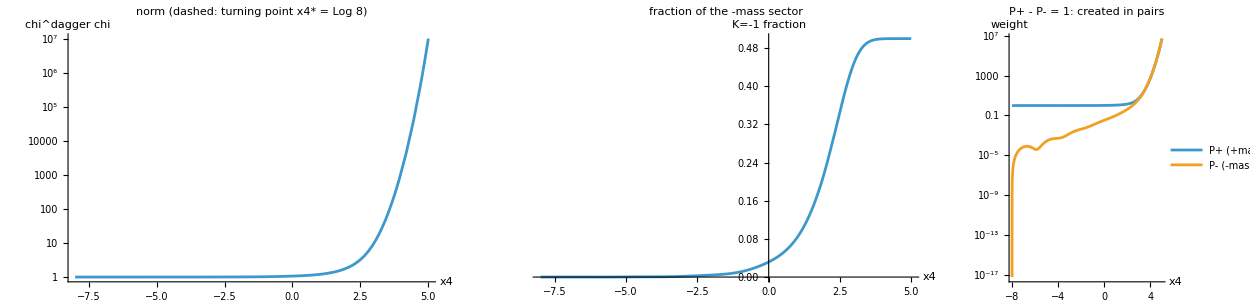

```mathematica
GraphicsRow[{LogPlot[normAt[x], {x, -8, 5}, PlotRange -> All, AxesLabel -> {"x4", "chi^dagger chi"}, PlotLabel -> "norm (dashed: turning point x4* = Log 8)", GridLines -> {{x4star}, None}, GridLinesStyle -> Dashed],
  Plot[minusFrac[x], {x, -8, 5}, PlotRange -> All, AxesLabel -> {"x4", "K=-1 fraction"}, PlotLabel -> "fraction of the -mass sector"],
  LogPlot[{plusW[x], minusW[x]}, {x, -8, 5}, PlotRange -> All, AxesLabel -> {"x4", "weight"}, PlotLegends -> Placed[{"P+ (+mass)", "P- (-mass)"}, {Left, Top}], PlotLabel -> "P+ - P- = 1: created in pairs"]}, ImageSize -> 1250]
```

## Part 9. Pairs of +mass and -mass universes in the deflation field

(i) Mass-sign pairing: C psi = Gamma psi^* and P1 psi(x) = T^1 psi(R1 x) map solutions with mass +m onto solutions with mass -m (exact, Part 7). (ii) Frequency pairing: the field equation has real coefficients, so complex conjugation maps a mode of frequency omega onto one of frequency -omega. (iii) Mixing of the two mirror sectors: with K = -I sigma16.T^4, the Lagrangian has no cross terms between psi_+ and psi_- from the directions x0..x4, while the deflating directions x5, x6, x7 couple the sectors with the GROWING coefficients E^(a x4/2)/Sqrt[bjj]. Deflation therefore mixes +mass and -mass universes ever more strongly (Part 8, K=-1 fraction).

```mathematica
crossD[A_] := Simplify[(ID16 + K).sigma16.(cD[[A + 1]] T16A[A]).(ID16 - K), assumD];
<|"no + / - cross term from direction A (A = 0..7)" -> Table[AllTrue[Flatten[crossD[A]], # === 0 &], {A, 0, 7}],
 "magnitudes of the cross-term entries for A = 5, 6, 7" -> Table[Union[Simplify[Abs[Flatten[crossD[A]]], assumD]], {A, 5, 7}]|>
```

<|no + / - cross term from direction A (A = 0..7)→{True,True,True,True,True,False,False,False},magnitudes of the cross-term entries for A = 5, 6, 7→{{0,(2 ⅇ^((a x4)/2))/(√b55)},{0,(2 ⅇ^((a x4)/2))/(√b66)},{0,(2 ⅇ^((a x4)/2))/(√b77)}}|>

(iv) Exact pair creation: conservation of the Krein charge. A mode of the pure deflation field (and every frozen-coefficient mode of Part 8) obeys chi' = M chi with M = T^4 (I Sum_(A != 4) kappa_A T^A - m), kappa_A = c_A k_A real. Because M^dagger K + K M = 0, the Krein charge Q = chi^dagger K chi = P+ - P- is conserved; here P+ and P- are the weights of the +mass (K = +1) and -mass (K = -1) sectors, and Q is the x4-component of the conserved current psibar gamma^mu psi of dirac16complex (sigma16.T^4 = I K, gamma^4 = T^4). The norm N = P+ + P- changes only through M^dagger + M = 2 I T^4 (kappa_5 T^5 + kappa_6 T^6 + kappa_7 T^7), i.e. only through the deflating directions, and this generator anticommutes with K: it creates +mass and -mass weight together. Hence P+ = (N + Q)/2 and P- = (N - Q)/2 grow by exactly the same amount: deflation creates {+mass, -mass} universes in pairs (numerically Q = 1 to within 2.2*10^-7 at x4 = -8, 0, x4*, 3, 5, and the K = -1 fraction equals (N - 1)/(2 N) to within 7.2*10^-7 on the grid x4 = -8, -7, ..., 5; Part 8).

```mathematica
kapA = {kap0, kap1, kap2, kap3, 0, kap5, kap6, kap7};      (* kappa_A = c_A k_A : arbitrary real numbers *)
Mdef = T16A[4].(I Sum[kapA[[A + 1]] T16A[A], {A, 0, 7}] - m ID16);
MdefH = ComplexExpand[ConjugateTranspose[Mdef]];         (* all symbols real *)
<|"sigma16.T^4 == I K" -> (sigma16.T16A[4] === I K),
 "M^dagger K + K M == 0 (Krein charge chi^dagger K chi conserved)" -> (Simplify[MdefH.K + K.Mdef] === ConstantArray[0, {16, 16}]),
 "M^dagger + M == 2 I T^4 (kap5 T^5 + kap6 T^6 + kap7 T^7)" -> (Simplify[MdefH + Mdef - 2 I T16A[4].(kap5 T16A[5] + kap6 T16A[6] + kap7 T16A[7])] === ConstantArray[0, {16, 16}]),
 "the norm-changing generator anticommutes with K" -> (Simplify[K.(MdefH + Mdef) + (MdefH + Mdef).K] === ConstantArray[0, {16, 16}])|>
```

<|sigma16.T^4 == I K→True,M^dagger K + K M == 0 (Krein charge chi^dagger K chi conserved)→True,M^dagger + M == 2 I T^4 (kap5 T^5 + kap6 T^6 + kap7 T^7)→True,the norm-changing generator anticommutes with K→True|>

## Part 10. Results

1. Metric and proper sizes (Part 4): the deflating degrees of freedom x5, x6, x7 have metric components -g55, -g66, -g77 with gjj = bjj E^(-a x4), proper sizes Sqrt[bjj] E^(-a x4/2) per unit coordinate interval, deflation rate d ln L/dx4 = -a/2 and e-folding time 2/a; Sqrt|g| = Sqrt[b55 b66 b77] Tan[6Hx0] Sin[6Hx0]^(-1/2) E^(-3(H + a/2) x4).
2. Curvature (Part 5): the Ricci scalar, the Einstein tensor and the Kretschmann scalar of the full field are computed exactly; the only non-zero off-diagonal Ricci component is R_04 = -3 H^2 Cot[6Hx0], it does not contain a, and G_04 = R_04. All of them depend on x0 only, not on x4, so deflation creates no curvature singularity at any finite x4. Near x0 = 0, R = -7/(108 H^2 x0^4) and R_abcd R^abcd = 85/(69984 H^4 x0^8) to leading order, independent of a: the curvature singularity at x0 = 0 of the primordial field remains. The pure deflation field is flat R^4 (x0..x3) times the block (x4, x5, x6, x7), which is maximally symmetric, R_abcd = (a^2/4)(g_ac g_bd - g_ad g_bc): with w = (2/a) E^(a x4/2) and yj = Sqrt[bjj] xj its metric is -(4/a^2)(dw^2 + dy5^2 + dy6^2 + dy7^2)/w^2, the hyperbolic 4-space H^4 of radius 2/a with all four directions timelike. Hence R = 3 a^2, R_abcd R^abcd = 3 a^4/2 and G^mu_mu = -3a^2/2 (mu = 0..3), -3a^2/4 (mu = 4..7) are constant.
3. Geodesics (Part 6): a world line with momentum p5 along a deflating direction has dx5/dlambda = -(p5/b55) E^(a x4) and (dx4/dlambda)^2 = 1 - (p5^2/b55) E^(a x4); it turns back at x4* = (1/a) Log[b55/p5^2]. In the hyperbolic block it is a semicircle of radius w* = 2 Sqrt[b55]/(a |p5|) standing on w = 0, with its top at x4*.
4. Field equation of dirac16complex (exact Grassmann derivation, Part 7): Cot[6Hx0] T^0 d0 psi + E^(H x4) Sin[6Hx0]^(1/6) Sum_i T^i d_i psi + T^4 d4 psi + E^(a x4/2) Sum_j T^j d_j psi/Sqrt[bjj] - (3/2) H Cot[6Hx0]^2 T^0 psi - (3/2)(H + a/2) T^4 psi = (m + lam psibar psi) psi; gamma^mu is covariantly constant, the Lagrangian is real, and the mass-sign maps C and P1 hold. The rescaling psi = Sin[6Hx0]^(1/4) E^(3(a + 2H) x4/4) chi removes both friction terms exactly (Part 8).
5. Universes (Part 8): omega^2 = m^2 + Cot[6Hx0]^2 k0^2 + E^(2Hx4) Sin[6Hx0]^(1/3) Sum k_i^2 - E^(a x4) Sum q_j^2/bjj. For k_i = 0, omega^2 decreases strictly and vanishes only at x4* = (1/a) Log[(m^2 + Cot[6Hx0]^2 k0^2)/Sum q_j^2/bjj], where the universe turns from oscillating to exponentially growing. The critical deflation rate is a_c = 2H; at a = 2H the late-time sign of omega^2 is that of Sin[6Hx0]^(1/3) Sum k_i^2 - Sum q_j^2/bjj. The exact numerical evolution (a = b55 = k = m = 1, q = 1/2, x4* = Log 8 = 2.0794) confirms it: the norm chi^dagger chi is 1 at x4 = -8, 1.0674 at x4 = 0, 1.9673 at x4*, 10.010 at x4 = 3, 1198.2 at x4 = 4 and 1.0588*10^7 at x4 = 5.
6. Pairs (Parts 8-9): directions x0..x4 produce no cross terms between the +mass and -mass sectors, while the deflating directions couple them with the growing coefficients E^(a x4/2)/Sqrt[bjj]. The Krein charge Q = P+ - P- = chi^dagger K chi is exactly conserved (M^dagger K + K M = 0), and the norm N = P+ + P- changes only through the deflating directions, by a generator that anticommutes with K. Therefore the +mass weight P+ = (N + Q)/2 and the -mass weight P- = (N - Q)/2 grow by exactly the same amount. In the example Q = 1 (the values computed at x4 = -8, 0, x4*, 3, 5 deviate from 1 by less than 2.2*10^-7); P- = 1.2*10^-31, 0.0337, 0.4836, 4.5051, 5.293976*10^6 and P+ = 1, 1.0337, 1.4836, 5.5051, 5.293977*10^6 at x4 = -8, 0, x4*, 3, 5. The K = -1 fraction, equal to (N - 1)/(2N) within 7.2*10^-7, is 1.2*10^-31 at x4 = -8, 0.0316 at x4 = 0, 0.2458 at x4*, 0.4501 at x4 = 3 and 0.49999995 at x4 = 5. Deflation creates {+mass, -mass} universes in pairs.